# Distorted Wave Born Approximation

```mathematica
WS[r_,V_,R_,a_]:=V/(1+Exp[(r-R)/a])
Col[r_,Z1_,Z2_,A_,Rc_]:=ee Z1 Z2 Piecewise[{{1/r,r>Rc A^(1/3)},{1/2(3/(Rc A^(1/3))-r^2/(Rc^3 A)),r≤ Rc A^(1/3)}}]
ℏ=197.3269788; (* MeV fm /c^2*)
ee=ℏ/137;
mp=938.272; 
m23F=21423.077578;
SphericalBesselH[l_,k_,r_,β_]:=k r SphericalBesselJ[l, k r]-β k r SphericalBesselY[l,k r] 
η[Z_,E_,mμ_]:=1.44/ℏ Z mμ/(√(2 mμ E))
CoulombPS[L_,η_]:=Arg[Gamma[1+L+ⅈ η]];
HL[L_,η_,ρ_,sign_]:=Exp[sign ⅈ (ρ-L π/2+CoulombPS[L,η]-η Log[2 ρ])]((-sign)2 ⅈ ρ)^(1+L + ⅈ η)HypergeometricU[1+L+sign ⅈ η,2L+2,-sign 2ⅈ ρ]
FL[L_,η_,ρ_]:=Re[HL[L,η,ρ,1]]
GL[L_,η_,ρ_]:=Im[HL[L,η,ρ,1]]
PartialWave[pot_Symbol,m1_,Z1_,m2_,Z2_,T_,L_,rRange_,nStep_, rPS_,plotFlag_]:=Module[
{s,f,mμ,normDW,normG,PW,α,β,δ,u, KEcm, k, HD, PS,r},
KEcm=0;
mμ=m1;
k=(√(2m1 T))/ℏ;
s=NDSolve[{u''[r]==(2mμ)/ℏ^2(pot[r]-T)u[r]+(L(L+1))/r^2 u[r], u[0.1]==0,u'[0.1]==1},u,{r,0.1,rRange}][[1]];
f[r_]:=u[r]/.s;
normDW=NMaximize[{f[r],0.1<r<rRange},r][[1]];
normG=FindMaximum[GL[L,η[Z1 Z2,T,mμ],k r],{r,rPS}][[1]];
Print[{normG,normDW}];
PW=Table[Flatten[{r,f[r] normG/normDW}],{r,0.1,rRange,nStep}];
HD=D[HL[L,η[Z1 Z2,T,mμ],k r,1],r]/.r->rPS;
PS={αj,βj}/.NSolve[{
f[rPS] normG/normDW==αj(GL[L,η[Z1 Z2,T,mμ],k rPS]+βj FL[L,η[Z1 Z2,T,mμ],k rPS]),
(D[f[r],r]/.r->rPS)normG/normDW==αj(Im[HD]+βj Re[HD])
},{αj,βj}];
(*Print[PS];*)
β=PS[[1,2]];
α=PS[[1,1]];
δ=ArcTan[β];
If[plotFlag==1,
Print[
Plot[{
f[r] normG/normDW ,
GL[L,η[Z1 Z2,T,mμ],k r],
α(GL[L,η[Z1 Z2,T,mμ],k r]+β FL[L,η[Z1 Z2,T,mμ],k r])
},{r,0.1,rRange},PlotStyle->{Directive[Blue,Thick],Green,Red}]];
];
{PW,k,β,δ}
]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.03192,2.20512×10^14}

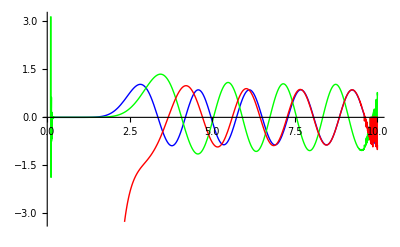

{4.27942,2.09312,1.1251}

```mathematica
Upot[r_]:=WS[r,-50,5,1]+Col[r,1,1,1,1.25]
(*Upot[r_]:=-60Exp[-r^2/4.5^2]+4 1.44Piecewise[{{1/r,r>4.5},{1/(2 4.5)(3-r^2/4.5^2),r≤ 4.5}}]*)(*WS[r,60,2,0.2]*)
L=12;
L0=PartialWave[Upot,3.8mp,2,3.8mp,2,100,L,10,0.1,9,1];
L0[[2;;-1]]
```

```mathematica
βMatrix=Monitor[
Table[
L0=PartialWave[Upot,3.8mp,2,3.8mp,2,100,ll,10,0.1,9,0];
{ll,L0[[-2]]},{ll,0,20}]
,ll]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.00035,0.205789}

{1.00013,0.440289}

{1.47193,2.26279}

{1.02618,20.8654}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.667627,288.48}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

{1.0005,4614.57}

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{0.655653,107143.}

{1.01211,2.72653×10^6}

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{6317.78,8.07729×10^7}

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMaximum :: sdprec will be suppressed during this calculation.

{0.165318,2.74009×10^9}

{0.,1.05114×10^11}

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -17791\ αj/18457 + 151145\ βj/110742 == 1.

{1.04501,4.51543×10^12}

{1.03192,2.15507×10^14}

{1.02536,1.13539×10^16}

{1.03763,6.56744×10^17}

{0.,4.15114×10^19}

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -17791\ αj/18457 + 151145\ βj/110742 == 1.

{1.40308,2.85519×10^21}

{795664.,2.12867×10^23}

{1.42601,1.71381×10^25}

FindMaximum::fmdig: Working precision MachinePrecision is insufficient to achieve the requested accuracy or precision.

{1.13013,1.48453×10^27}

{1.44715,1.37836×10^29}

{{0,4.69933},{1,-6.95224},{2,-10.3859},{3,-784.327},{4,10.9709},{5,4.86831},{6,3.06988},{7,2.067},{8,1.50434},{9,1.08135},{10,0.732687},{11,0.525553},{12,0.311695},{13,0.106821},{14,-0.0941673},{15,0.732687},{16,-0.56006},{17,-0.866966},{18,-1.33995},{19,-2.12372},{20,-4.09715}}

```mathematica
δMatrix=Table[{βMatrix[[i,1]],ArcTan[βMatrix[[i,2]]]},{i,1,Length[βMatrix]}]
```

{{0,1.36113},{1,-1.42794},{2,-1.47481},{3,-1.56952},{4,1.4799},{5,1.3682},{6,1.25589},{7,1.1202},{8,0.984127},{9,0.824466},{10,0.632329},{11,0.48388},{12,0.302151},{13,0.106418},{14,-0.0938904},{15,0.632329},{16,-0.510534},{17,-0.714262},{18,-0.929668},{19,-1.13072},{20,-1.3314}}

```mathematica
(* Regulate Phase Shift *)
shift={1,2,3};
Table[δMatrix[[i,2]]=δMatrix[[i,2]]+π,{i,shift}]
```

{5.35781,5.34498,4.97478}

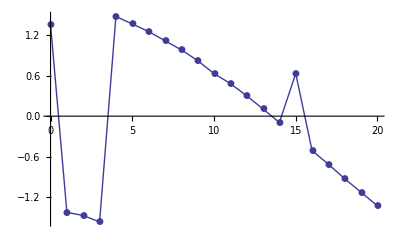

```mathematica
ListPlot[δMatrix,Joined->True,PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
SMatrix=Table[{δMatrix[[i,1]],1-Exp[ⅈ 2 δMatrix[[i,2]]]},{i,1,Length[δMatrix]}]
```

{{0,1.27631+0.961067 ⅈ},{1,1.30089+0.95366 ⅈ},{2,1.86543+0.501028 ⅈ},{3,1.92-0.391917 ⅈ},{4,0.337894-0.74941 ⅈ},{5,0.249826+0.66124 ⅈ},{6,0.0789186-0.38937 ⅈ},{7,0.00297006-0.077015 ⅈ},{8,0.000191004-0.0195441 ⅈ},{9,0.0000136221-0.00521958 ⅈ},{10,9.69218×10^-7-0.00139228 ⅈ},{11,6.42062×10^-8-0.000358347 ⅈ},{12,3.71798×10^-9-0.000086232 ⅈ},{13,1.78643×10^-10-0.000018902 ⅈ},{14,6.90203×10^-12-3.7154×10^-6 ⅈ},{15,2.11053×10^-13-6.49779×10^-7 ⅈ},{16,0.+0. ⅈ},{17,0.+0. ⅈ},{18,0.+0. ⅈ},{19,0.+0. ⅈ},{20,0.+0. ⅈ}}

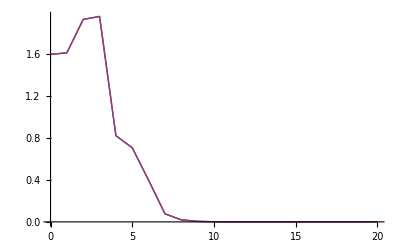

```mathematica
ListPlot[{
Table[{SMatrix[[i,1]],Norm[SMatrix[[i,2]]]},{i,1,Length[SMatrix]}],
Table[{SMatrix[[i,1]],Norm[1-Exp[ⅈ 2 ArcTan[βMatrix[[i,2]]]]]},{i,1,Length[SMatrix]}]
},Joined->True]
```